```mathematica
RSolve[{a[n]==2 a[n-1],a[1]==1},a[n],n]
```

{{a[n]→2^(-1+n)}}

```mathematica
RSolve[{t[u]==t[u-1] + u ^2,t[1]==1},t[n],n]
```

RSolve::deqx: Supplied equations are not difference equations of the given functions.

RSolve[{t[u]==u^2+t[-1+u],t[1]==1},t[n],n]

```mathematica
T[1]=1
T[n_]:=T[n-1]+n^2
Table[T[n],{n,1,100,2}]
```

1

{1,14,55,140,285,506,819,1240,1785,2470,3311,4324,5525,6930,8555,10416,12529,14910,17575,20540,23821,27434,31395,35720,40425,45526,51039,56980,63365,70210,77531,85344,93665,102510,111895,121836,132349,143450,155155,167480,180441,194054,208335,223300,238965,255346,272459,290320,308945,328350}

```mathematica
Table[n^2,{n,1,100,2}]
```

{1,9,25,49,81,121,169,225,289,361,441,529,625,729,841,961,1089,1225,1369,1521,1681,1849,2025,2209,2401,2601,2809,3025,3249,3481,3721,3969,4225,4489,4761,5041,5329,5625,5929,6241,6561,6889,7225,7569,7921,8281,8649,9025,9409,9801}

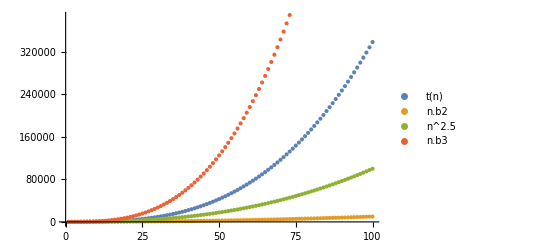

```mathematica
ListPlot[{Table[T[n],{n,1,100,1}], Table[n^2,{n,1,100,1}], Table[n^2.5,{n,1,100,1}], Table[n^3,{n,1,100,1}]} , AxesLabel->Automatic, PlotLegends->{"t(n)", "n.b2","n^2.5", "n.b3"}]
```